```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\蛋白质浓度测量\\Lowry.xlsx"]
```

```mathematica
data3={{0.,0.},{20.,0.047},{40.,0.096},{80.,0.177},{120.,0.25},{160.,0.319},{200.,0.3775}}
```

{{0.,0.},{20.,0.047},{40.,0.096},{80.,0.177},{120.,0.25},{160.,0.319},{200.,0.3775}}

```mathematica
lm3=LinearModelFit[data3,x,x]
```

FittedModel[0.0134855+0.00189049 x]

```mathematica
Normal[lm3]
```

0.0134855+0.00189049 x

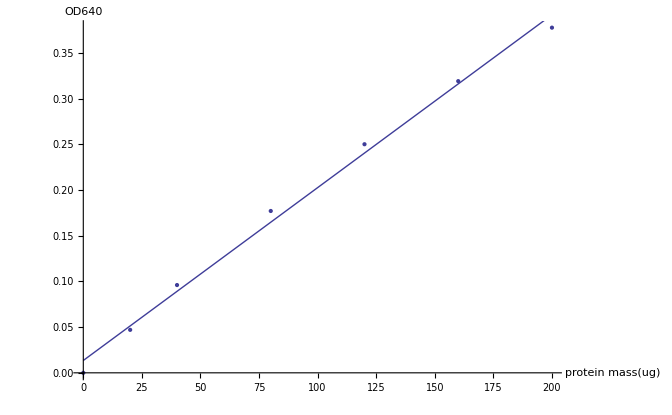

```mathematica
Show[ListPlot[data3],Plot[lm3[x],{x,0,200}],AxesLabel-> {"protein mass(ug)","OD640"}]
```

```mathematica
lm3["RSquared"]
```

0.99419